```mathematica
SetDirectory["/home/eva/Documents/ITMO/4_course/tou/lab2/code"];
```

```mathematica
T=9;

sol=DSolve[
{
x1'[t]==x2[t],
x2'[t]==-5 x2[t]+phi2[t]/10,

phi1'[t]==0,
phi2'[t]==-phi1[t]+5 phi2[t],

x1[0]==0,x2[0]==0,
x1[T]==1,x2[T]==0
},

{x1,x2,phi1,phi2},t
];

psi1_opt=phi1[0]/.sol[[1]]
psi2_opt=phi2[0]/.sol[[1]]
```

(1250 (1+ⅇ^45))/(47+43 ⅇ^45)

-(250 (1-ⅇ^45))/(47+43 ⅇ^45)

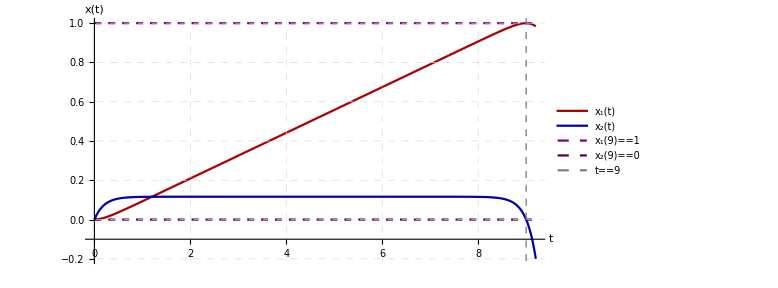

```mathematica
X1 = x1[t]/.sol[[1]];
X2 = x2[t]/.sol[[1]];

plotX = Plot[
{X1 ,X2, 1, 0, ConditionalExpression[Null,True]},{t,0,T+0.2}, 

Epilog->{
Directive[Gray,Dashed],
InfiniteLine[{9,0},{0,1}]
},

Ticks->{Range[0,T],Automatic},

PlotRangePadding->{Automatic,Scaled[0.1]},

AxesOrigin->{0,-0.1},

PlotLegends->Placed[{
ExpressionCell[ToExpression["x_1(t)",TeXForm],"StandardForm", FontFamily->"Cambria Math",FontSize->18],
ExpressionCell[ToExpression["x_2(t)",TeXForm],"StandardForm", FontFamily->"Cambria Math",FontSize->18],
ExpressionCell[ToExpression["x_1(9)=1",TeXForm],"StandardForm", FontFamily->"Cambria Math",FontSize->18],
ExpressionCell[ToExpression["x_2(9)=0",TeXForm],"StandardForm", FontFamily->"Cambria Math",FontSize->18],
ExpressionCell[ToExpression["t=9",TeXForm],"StandardForm", FontFamily->"Cambria Math",FontSize->18]
}, Right],

BaseStyle->{FontFamily->"Cambria Math",FontSize->16},

 AxesLabel->{
ExpressionCell[ToExpression["t",TeXForm],"StandardForm", FontFamily->"Cambria Math",FontSize->18],
ExpressionCell[ToExpression["x(t)",TeXForm],"StandardForm", FontFamily->"Cambria Math",FontSize->18],
},

AxesStyle->Directive[Darker[Gray],15, Arrowheads[0.03]],

PlotStyle->{
{Darker[Red], Thick},
{Darker[Blue], Thick},
{Purple, Dashed},
{Darker[Purple], Dashed},
{Gray,Dashed}
},

GridLines->{
Range[0,T,2],
Range[-0.6,5,0.2]
},

GridLinesStyle->Directive[LightGray,Dashed],

AspectRatio-> 0.5, 
ImageSize->Large

]

Export["../report/images/x.pdf",plotX,ImageResolution->600];
```

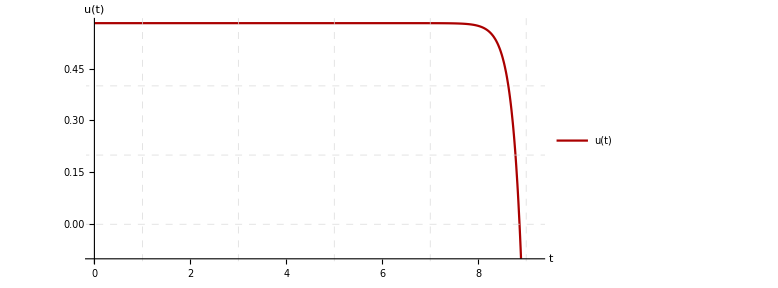

```mathematica
U =(phi2[t]/.sol[[1]])/10;

plotU = Plot[U, {t,0,T+0.2},

Ticks->{Range[0,T],Automatic},

PlotRangePadding->{Automatic,Scaled[0.1]},

AxesOrigin->{0,-0.1},

PlotLegends->Placed[{
ExpressionCell[ToExpression["u(t)",TeXForm],"StandardForm", FontFamily->"Cambria Math",FontSize->18]
}, Right],

BaseStyle->{FontFamily->"Cambria Math",FontSize->16},

 AxesLabel->{
ExpressionCell[ToExpression["t",TeXForm],"StandardForm", FontFamily->"Cambria Math",FontSize->18],
ExpressionCell[ToExpression["u(t)",TeXForm],"StandardForm", FontFamily->"Cambria Math",FontSize->18],
},

AxesStyle->Directive[Darker[Gray],15, Arrowheads[0.03]],

PlotStyle->{Darker[Red], Thick},

GridLines->{
Range[1,T,2],
Range[-0.6,5,0.2]
},

GridLinesStyle->Directive[LightGray,Dashed],

AspectRatio-> 0.5, 
ImageSize->Large
]

Export["../report/images/u.pdf",plotU,ImageResolution->600];
```

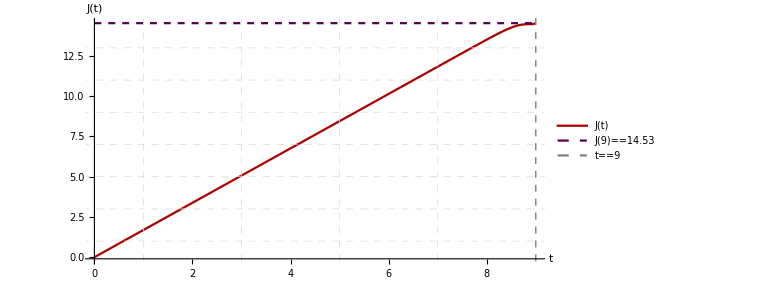

```mathematica
JAccumulated[tau_]:=NIntegrate[5*(U/.t->s)^2,{s,0,tau}];

plotJ = Plot[{JAccumulated[τ], JAccumulated[9], ConditionalExpression[Null,True]},{τ,0,9},

Epilog->{
Directive[Gray,Dashed],
InfiniteLine[{9,0},{0,1}]
},

Ticks->{Range[0,T],Automatic},

PlotRangePadding->{Automatic,Scaled[0.1]},

AxesOrigin->{0,-0.1},

PlotLegends->Placed[{
ExpressionCell[ToExpression["{J}(t)",TeXForm],"StandardForm", FontFamily->"Cambria Math",FontSize->18],
ExpressionCell[ToExpression["J(9) = 14.53",TeXForm],"StandardForm", FontFamily->"Cambria Math",FontSize->18],
ExpressionCell[ToExpression["t=9",TeXForm],"StandardForm", FontFamily->"Cambria Math",FontSize->18]
}, Right],

BaseStyle->{FontFamily->"Cambria Math",FontSize->16},

 AxesLabel->{
ExpressionCell[ToExpression["t",TeXForm],"StandardForm", FontFamily->"Cambria Math",FontSize->18],
ExpressionCell[ToExpression["{J}(t)",TeXForm],"StandardForm", FontFamily->"Cambria Math",FontSize->18]
},

AxesStyle->Directive[Darker[Gray],15, Arrowheads[0.03]],

PlotStyle->{
{Darker[Red], Thick},
{Darker[Purple], Dashed},
{Gray, Dashed}
},

GridLines->{
Range[1,T,2],
Range[-1,20,2]
},

GridLinesStyle->Directive[LightGray,Dashed],

AspectRatio-> 0.5, 
ImageSize->Large
]

Export["../report/images/J.pdf",plotJ,ImageResolution->600];
```

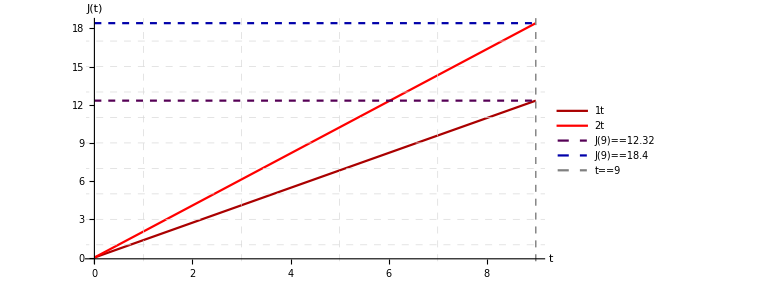

1.36898 tau

2.04502 tau

```mathematica
U2 =(phi2[0]/.sol[[1]])/10*0.9;

U3=(phi2[0]/.sol[[1]])/10*1.1;

J2[tau_]:=NIntegrate[5*(U2/.t->s)^2,{s,0,tau}];

J3[tau_]:=NIntegrate[5*(U3/.t->s)^2,{s,0,tau}];

plotJ2 = Plot[{J2[τ], J3[τ], J2[9], J3[9], ConditionalExpression[Null,True]},{τ,0,9},

Epilog->{
Directive[Gray,Dashed],
InfiniteLine[{9,0},{0,1}]
},

Ticks->{Range[0,T],Automatic},

PlotRangePadding->{Automatic,Scaled[0.1]},

AxesOrigin->{0,-0.1},

PlotLegends->Placed[{
ExpressionCell[ToExpression["{J_1}(t)",TeXForm],"StandardForm", FontFamily->"Cambria Math",FontSize->18],
ExpressionCell[ToExpression["{J_2}(t)",TeXForm],"StandardForm", FontFamily->"Cambria Math",FontSize->18],
ExpressionCell[ToExpression["J(9) = 12.32",TeXForm],"StandardForm", FontFamily->"Cambria Math",FontSize->18],
ExpressionCell[ToExpression["J(9) = 18.40",TeXForm],"StandardForm", FontFamily->"Cambria Math",FontSize->18],
ExpressionCell[ToExpression["t=9",TeXForm],"StandardForm", FontFamily->"Cambria Math",FontSize->18]
}, Right],

BaseStyle->{FontFamily->"Cambria Math",FontSize->16},

 AxesLabel->{
ExpressionCell[ToExpression["t",TeXForm],"StandardForm", FontFamily->"Cambria Math",FontSize->18],
ExpressionCell[ToExpression["{J}(t)",TeXForm],"StandardForm", FontFamily->"Cambria Math",FontSize->18]
},

AxesStyle->Directive[Darker[Gray],15, Arrowheads[0.03]],

PlotStyle->{
{Darker[Red], Thick},
{Red, Thick},
{Darker[Purple], Dashed},
{Darker[Blue], Dashed},
{Gray, Dashed}
},

GridLines->{
Range[1,T,2],
Range[-1,20,2]
},

GridLinesStyle->Directive[LightGray,Dashed],

AspectRatio-> 0.5, 
ImageSize->Large
]

Export["../report/images/J12.pdf",plotJ2,ImageResolution->600];


J2[tau_]:=Integrate[5*(U2/.t->s)^2,{s,0,tau}];
J3[tau_]:=Integrate[5*(U3/.t->s)^2,{s,0,tau}];

J2[tau]
J3[tau]
```